```mathematica
f[x_] = c1*x/(c2+c1*x)
```

(c1 x)/(c2+c1 x)

```mathematica
FullSimplify[D[f[x],x]]
```

(c1 c2)/(c2+c1 x)^2

```mathematica
ϵE[p_,α_] := (ΛH/(h + p))*(1 - Exp[(-(h + p))*α])
```

```mathematica
FullSimplify[D[ϵE[p,α],α]+(h+p)ϵE[p,α]-ΛH]
```

0

```mathematica
ϵD[p_,α_] := (ⅇ^(-(p+rD) α) h (h-ⅇ^((p+rD) α) h+p+ⅇ^((p+rD) α) rD-ⅇ^((-h+rD) α) (p+rD)) ΛH ρ)/((h+p) (-h+rD) (p+rD))
```

```mathematica
FullSimplify[D[ϵD[p,α],α]-ρ*h*ϵE[p,α]+(rD+p)*ϵD[α]]
```

0

```mathematica
ϵA[p_,α_]:=1/(h+p)ⅇ^(-(p+rA) α) h ΛH (((h+p) rD ρ (-1+ϕ))/((h-rD) (p+rD) (-rA+rD))+(rD+h (-1+ρ)-rD ρ ϕ)/((h-rA) (h-rD))+(p (-1+ρ)+rD (-1+ρ ϕ))/((p+rA) (p+rD))+ⅇ^((p+rA) α) ((ⅇ^(-(p+rD) α) (h+p) rD ρ (-1+ϕ))/((-h+rD) (p+rD) (-rA+rD))+(p+rD-p ρ-rD ρ ϕ)/((p+rA) (p+rD))+(ⅇ^(-(h+p) α) (h-h ρ+rD (-1+ρ ϕ)))/((h-rA) (h-rD))))
```

```mathematica
FullSimplify[D[ϵA[p,α],α]-(1-ρ)*h*ϵE[p,α]-(1-ϕ)*rD*ϵD[α]+(rA+p)*ϵA[α]]
```

0

### Analysis of the Characteristic Equation

```mathematica
αmax = 80
```

80

```mathematica
F[p_,α_]:=ϵD[p,α]/ΛH
```

```mathematica
H[p_,α_]:=ϵA[p,α]/ΛH
```

```mathematica
q=3.110839319579504*10^(-5)
```

0.0000311084

```mathematica
Mint[α_,b0_,b1_,b2_,b3_,b4_]:=(α/365)*b0+(b1/b2)*(1-Exp[-b2*α/365])+(b3/b4)*(-1+Exp[b4*α/365])
```

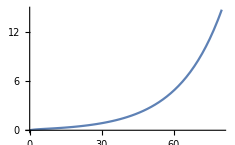

```mathematica
Plot[Mint[α*365,0,0.05,0.505,0.01,0.055],{α,0,80}]
```

```mathematica
K=1/NIntegrate[Exp[-Mint[α,0,0.05,0.505,0.01,0.055]-q*α],{α,0,αmax*365}]
```

0.000128232

```mathematica
Cstar[K_,bM_,bH_,βM_,gM_,σ_,μM_]:=K*bM*bH*βM*σ/(gM*(σ+μM))
```

```mathematica
{βD=0.35,βA=0.03,rD=1/180,rA=1/365,h=1/15,ρ=1/2,ϕ=1/2,bM=7,bH=18,βM=0.25,σ=1/10,gM=0.5,μM=1/10}
```

{0.35,0.03,1/180,1/365,1/15,1/2,1/2,7,18,0.25,1/10,0.5,1/10}

```mathematica
ζ[p_]:=Cstar[K,bM,bH,βM,gM,σ,μM]*NIntegrate[Exp[-Mint[α,0,0.05,0.505,0.01,0.055]-q*α]*(βD*F[p,α]+βA*H[p,α]),{α,0,αmax*365},Method->{"TrapezoidalRule","RombergQuadrature"->False},MaxRecursion->0]-1
```

```mathematica
Plot[ζ[p],{p,-0.01,0.01},PlotRange->Automatic]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in α near {α} = {29200.}. NIntegrate obtained 1.47189×10^89 and 1.47189×10^89 for the integral and error estimates.

-Graphics-

```mathematica
ζ[0]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in α near {α} = {29200.}. NIntegrate obtained 243920. and 58676.6 for the integral and error estimates.

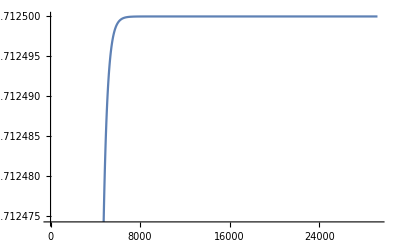

```mathematica
Plot[βD*F[0,α]+βA*H[0,α],{α,0,αmax*365}]
```

```mathematica
Cstar[K,bM,bH,βM,gM,σ,μM]
```

0.00403932